```mathematica
Plot3D[Sqrt[x+y+1]/(x-1),{x,-3,5},{y,-5,5},PlotRange->All,ImageSize->Scaled[0.75]]
```

-Graphics3D-

```mathematica
Plot3D[x Log[y^2-x],{x,-5,5},{y,-5,5},ImageSize->Scaled[0.75]]
```

-Graphics3D-

```mathematica
Plot3D[Sqrt[9-x^2-y^2],{x,-5,5},{y,-5,5},PlotRange->{0,3},ImageSize->Scaled[0.75]]
```

-Graphics3D-

-Graphics3D-

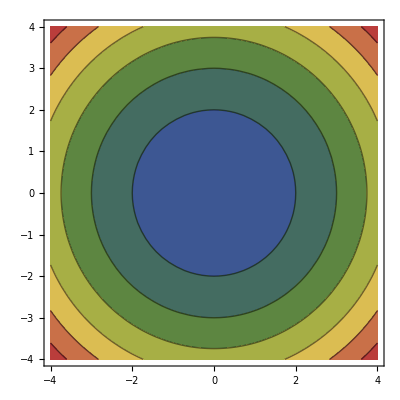

```mathematica
Plot3D[x^2+y^2-4,{x,-4,4},{y,-4,4},PlotRange->{-4,28},ClippingStyle->None,MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},Lighting->"Neutral",ImageSize->Scaled[0.75]]

ContourPlot[x^2+y^2-4,{x,-4,4},{y,-4,4},ColorFunction->"DarkRainbow",ImageSize->Scaled[0.75]]
```

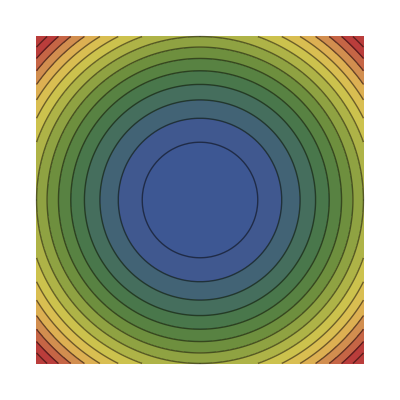

-Graphics3D-

-Graphics3D-

```mathematica
contourPotentialPlot1=ContourPlot[x^2+y^2-4,{x,-4,4},{y,-4,4},PlotRange->All,Contours->15,Axes->False,PlotPoints->30,PlotRangePadding->0,Frame->False,(* ContourShading->None, *)ColorFunction->"DarkRainbow"]

potential1=Plot3D[x^2+y^2-4,{x,-4,4},{y,-4,4},PlotRange->All,ClippingStyle->None,MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},Lighting->"Neutral"]

level=4;gr=Graphics3D[{Texture[contourPotentialPlot1],EdgeForm[],Polygon[{{-5,-5,level},{5,-5,level},{5,5,level},{-5,5,level}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral"];

Show[potential1,gr,PlotRange->All,BoxRatios->{1,1,.6},FaceGrids->{Back,Left},ImageSize->Scaled[1]]
```

```mathematica
?ColorFunction
```

ColorFunction is an option for graphics functions that specifies a function to apply to determine colors of elements.